```mathematica
filesAR=FileNames["/home/carla/GDC/CONF/DLB/GDC_Conf_AR_DLB_ALL_Out/*.txt"];
dataAR=Map[Get[#]&, filesAR];
filesBR=FileNames["/home/carla/GDC/CONF/DLB/GDC_Conf_BR_DLB_ALL_Out/*.txt"];
dataBR=Map[Get[#]&, filesBR];
```

```mathematica
confAR=dataAR[[All,1]]
confBR=dataBR[[All,1]]
```

{{{1.,1,1},{1.,1.,0.000341491},{1,1.,0.0000126478,0.000341491}},{{1.,1,1},{1.,1.,0.000436062},{1,1.,4.00793×10^-8,0.000436062}},{{0.00146843,1,681},{0.00119082,0.00146843,0.000277936},{0.682016,0.00146843,5.15678×10^-6,0.000277936}},{{0.00645161,1,155},{0.0061875,0.00645161,0.000265757},{0.921345,0.00645161,6.82174×10^-7,0.000265757}},{{0.00746269,5,670},{0.00703189,0.00746269,0.000433849},{0.890847,0.00746269,1.43745×10^-7,0.000433849}},{{0.00613497,5,815},{0.00580987,0.00613497,0.000326998},{0.899351,0.00613497,1.17189×10^-8,0.000326998}},{{0.028169,2,71},{0.0273054,0.028169,0.000887865},{0.940507,0.028169,1.03933×10^-10,0.000887865}},{{0.0344828,2,58},{0.0336203,0.0344828,0.000892412},{0.951201,0.0344828,1.24455×10^-11,0.000892412}},{{1.,1,1},{1.,1.,0.000435964},{1,1.,9.9865×10^-14,0.000435964}}}

{{{1.,160,160},{1.,1.,0.000436062},{1,1.,6.41268×10^-6,0.000436062}},{{1.,7,7},{1.,1.,0.000277936},{1,1.,5.30065×10^-8,0.000277936}},{{0.00146843,1,681},{0.00120299,0.00146843,0.000265757},{0.69382,0.00146843,2.99716×10^-6,0.000265757}},{{0.00645161,28,4340},{0.00617399,0.00645161,0.000279347},{0.917488,0.00645161,9.31121×10^-7,0.000279347}},{{0.00628931,78,12402},{0.00596426,0.00628931,0.000326998},{0.901714,0.00628931,1.78329×10^-7,0.000326998}},{{0.00452489,25,5525},{0.00431789,0.00452489,0.00020789},{0.912511,0.00452489,8.08775×10^-9,0.00020789}},{{0.00816327,2,245},{0.00727735,0.00816327,0.000892412},{0.804199,0.00816327,5.25713×10^-11,0.000892412}},{{0.0344828,2,58},{0.0336171,0.0344828,0.000895731},{0.951024,0.0344828,5.79217×10^-12,0.000895731}}}

```mathematica
dojCHEVBKAR=confAR[[All,1]][[All,1]]
dojCHAR=confAR[[All,2]][[All,3]]
dojEVBKAR=confAR[[All,3]][[All,3]]

dojCHEVBKBR=confBR[[All,1]][[All,1]]
dojCHBR=confBR[[All,2]][[All,3]]
dojEVBKBR=confBR[[All,3]][[All,3]]
```

{1.,1.,0.00146843,0.00645161,0.00746269,0.00613497,0.028169,0.0344828,1.}

{0.000341491,0.000436062,0.000277936,0.000265757,0.000433849,0.000326998,0.000887865,0.000892412,0.000435964}

{0.0000126478,4.00793×10^-8,5.15678×10^-6,6.82174×10^-7,1.43745×10^-7,1.17189×10^-8,1.03933×10^-10,1.24455×10^-11,9.9865×10^-14}

{1.,1.,0.00146843,0.00645161,0.00628931,0.00452489,0.00816327,0.0344828}

{0.000436062,0.000277936,0.000265757,0.000279347,0.000326998,0.00020789,0.000892412,0.000895731}

{6.41268×10^-6,5.30065×10^-8,2.99716×10^-6,9.31121×10^-7,1.78329×10^-7,8.08775×10^-9,5.25713×10^-11,5.79217×10^-12}

```mathematica
(*sList={"S0","S1","S2","S3","S4","S5","S6","S7","S8"};
dojP=Labeled[#[[1]],#[[2]]]&/@Map[{doj[[#]],sList[[#]]}&,ran]*)

sList={0,1,2,3,4,5,6,7,8};
sList2={0.5,1.5,2.5,3.5,4.5,5.5,6.5,7.5};
ran=Range[Length[sList]];
ran2=Range[Length[sList2]];

dojAAR={#[[2]],#[[1]]}&/@Map[{N[dojCHAR[[#]]/dojCHEVBKAR[[#]]],sList[[#]]}&,ran]
dojABR={#[[2]],#[[1]]}&/@Map[{N[dojCHBR[[#]]/dojCHEVBKBR[[#]]],sList2[[#]]}&,ran2]
dojPCHAR={#[[2]],#[[1]]}&/@Map[{dojCHAR[[#]],sList[[#]]}&,ran]
dojPCHBR={#[[2]],#[[1]]}&/@Map[{dojCHBR[[#]],sList2[[#]]}&,ran2]
dojPEVBKAR={#[[2]],#[[1]]}&/@Map[{dojEVBKAR[[#]],sList[[#]]}&,ran]
dojPEVBKBR={#[[2]],#[[1]]}&/@Map[{dojEVBKBR[[#]],sList2[[#]]}&,ran2]
```

{{0,0.000341491},{1,0.000436062},{2,0.189274},{3,0.0411924},{4,0.0581358},{5,0.0533007},{6,0.0315192},{7,0.0258799},{8,0.000435964}}

{{0.5,0.000436062},{1.5,0.000277936},{2.5,0.180981},{3.5,0.0432987},{4.5,0.0519928},{5.5,0.0459437},{6.5,0.10932},{7.5,0.0259762}}

{{0,0.000341491},{1,0.000436062},{2,0.000277936},{3,0.000265757},{4,0.000433849},{5,0.000326998},{6,0.000887865},{7,0.000892412},{8,0.000435964}}

{{0.5,0.000436062},{1.5,0.000277936},{2.5,0.000265757},{3.5,0.000279347},{4.5,0.000326998},{5.5,0.00020789},{6.5,0.000892412},{7.5,0.000895731}}

{{0,0.0000126478},{1,4.00793×10^-8},{2,5.15678×10^-6},{3,6.82174×10^-7},{4,1.43745×10^-7},{5,1.17189×10^-8},{6,1.03933×10^-10},{7,1.24455×10^-11},{8,9.9865×10^-14}}

{{0.5,6.41268×10^-6},{1.5,5.30065×10^-8},{2.5,2.99716×10^-6},{3.5,9.31121×10^-7},{4.5,1.78329×10^-7},{5.5,8.08775×10^-9},{6.5,5.25713×10^-11},{7.5,5.79217×10^-12}}

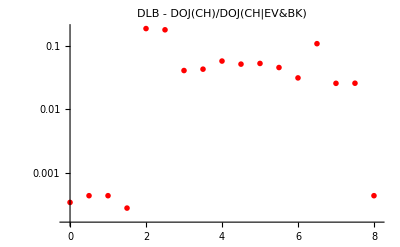

```mathematica
aPlot=ListLogPlot[{Union[dojAAR,dojABR]},  PlotLabel->"DLB - DOJ(CH)/DOJ(CH|EV&BK)", PlotRange->{{-0.1,8.1},All}, PlotStyle-> {Red}, PlotRange->All, PlotMarkers->{{"A",12}},ImageSize->400]
chPlot=ListLogPlot[{Union[dojPCHAR,dojPCHBR]}, PlotLegends->{"DOJ(CH)"}, PlotRange->{{-0.1,8.1},All}, PlotStyle-> {Red}, PlotRange->All, PlotLabel->"DLB - DOJ(CH)", PlotMarkers->{{"C",12}},ImageSize->400];
evbkPlot=ListLogPlot[{Union[dojPEVBKAR,dojPEVBKBR]}, PlotLegends->{"DOJ(EV&BK)"}, PlotRange->{{-0.1,8.1},All}, PlotStyle-> {Blue}, PlotRange->All, PlotLabel->"DLB - DOJ(EV&BK)", PlotMarkers->{{"E",12}},ImageSize->400];
allPlot=ListLogPlot[{Union[dojPCHAR,dojPCHBR], Union[dojPEVBKAR,dojPEVBKBR]}, PlotLegends->{"DOJ(CH)","DOJ(EV&BK)"}, PlotRange->{{-0.1,8.1},All}, PlotStyle-> {Red, Blue}, PlotRange->All, PlotLabel->"DLB - DOJ(CH),DOJ(EV&BK)", PlotMarkers->{{"C",12},{"E",12}},ImageSize->400];
plotsOut=Column[{chPlot,aPlot,evbkPlot} ];
```

```mathematica
SetDirectory["/home/carla/GDC/CONF/DLB/"];
Export["DLB_CH_EVBK.jpeg",plotsOut,ImageResolution->200]
Put[Union[dojPCHAR,dojPCHBR],"DLB_Z_APP.txt"]
Put[Union[dojAAR,dojABR],"DLB_F_APP.txt"]
```

DLB_CH_EVBK.jpeg

```mathematica
(*PlotParts=ListPlot[{Union[dojPAR,dojPBR], Union[zPAR,zPBR], Union[fPAR, fPBR]}, PlotLegends->{"DOJ","Z", "F"}, PlotStyle-> {Red, Blue, Yellow}, PlotRange->{0, 0.026},  PlotLabel->"DLB - DOJ, Z, F - Zoomed In",  PlotMarkers->{{"D",12},{"Z",12},{"F",12}}]
Export["DLB_Zoomed_In.jpeg",PlotParts,ImageSize->850]*)
```